```mathematica
Clear[f];
```

```mathematica
Vfene[r_, ϵ_, r0_, Δ_] := - (ϵ/2) Log[1 - ((r -r0)/Δ)^2];
Vmorse[x_, ϵ_, x0_, a_] := ϵ (1-Exp[ - a ( x - x0)])^2;
Vharm[r_, k_, r0_] := (k / 2) (r - r0)^2;
Vlj[r_, ϵ_, σ_] := 4 ϵ ( (σ/r)^12 - (σ/r)^6);
Vmod[θ_,a_,θ0_] := 1 - a(θ-θ0)^2;
Vsmooth[x_, b_, xc_] := b ( x-xc)^2;
```

```mathematica
dVljdr[x_,b_,xc_] := Evaluate[D[Vlj[x,b,xc],x]];
dVsdr[xx_,bx_, xxc_]:= Evaluate[D[Vsmooth[xx,bx,xxc],xx]];
```

```mathematica
ϵ=2; σ=0.7;rs=0.675;
```

```mathematica
myVar=FindRoot[ {
Evaluate[Vlj[rs,ϵ,σ]]==ϵ Vsmooth[rs,b, xc],
Evaluate[dVljdr[rs,ϵ,σ]]==ϵ dVsdr[rs,b, xc]
}, {{b,-1}, {xc, rs + 0.1}}, MaxIterations-> 3000];
Subscript[b, low]=b/.myVar
Subscript[xc, low]= xc/.myVar
```

892.016

0.711879

```mathematica
myVar=FindRoot[ 0==ϵ Vsmooth[x,Subscript[b, low], Subscript[xc, low]],{x,σ}, MaxIterations-> 10000];
rc=x/.myVar
```

0.711879

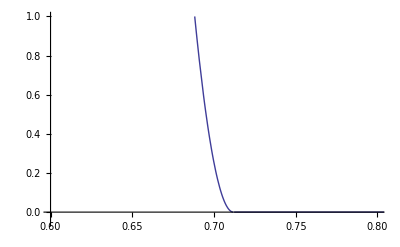

```mathematica
f2[r_] :=   Piecewise[{
{Vlj[r,ϵ,σ],r<rs},
{ϵ Vsmooth[r,Subscript[b, low],Subscript[xc, low]], rs <r < rc},
{0, rc < r}
}];
Plot[f2[r], {r, 0, 1}, PlotRange->{{σ-0.1,σ+0.1},{-0.05,1}}]
```